```mathematica
w=Simplify[∑_(m=1)^2 ∑_(n=1)^2 Subscript[A, m,n] Sin[(m π x)/a]Sin[(n π y)/b]];
```

```mathematica
Модуль Юнга e = 7.05*10^10 Па
Коэффициент Пуассона ν = 0.345
Толщина пластины h = 0.001 метров
Длина a = 0.4 м
Ширина b = 0.5 м
Распределённая нагрузка q = 1 Н/м
```

```mathematica
d1=(e*h^3)/(12*(1-ν^2))/.{e->7.05*10^10,h->0.001,ν->0.345};
```

```mathematica
d1
```

6.66875

```mathematica
Проверка граничных условий:
x = 0 и x = a
```

```mathematica
w/.x->0
w/.x->a
D[w, x,x] /.x->0
D[w, x,x]/.x->a
D[w, y,y]/.x->0
D[w, y,y]/.x->a
```

0

0

0

«3 more identical outputs»

```mathematica
y = 0 и y = b
```

```mathematica
w/.y->0
w/.y->b
D[w, x,x] /.y->0
D[w, x,x]/.y->b
D[w, y,y]/.y->0
D[w, y,y]/.y->b
```

0

0

0

«3 more identical outputs»

```mathematica
q==Simplify[d Laplacian[Laplacian[w,{x,y}],{x,y}]];
```

```mathematica
Разложение нагрузки в двойной тригонометрический ряд Фурье по синусам на прямоугольной области:
```

```mathematica
0≤x≤a;
0≤y≤b;
```

```mathematica
q== Simplify[∑_(m=1)^2 ∑_(n=1)^2 Subscript[С, mn] Sin[(m π x)/a]Sin[(n π y)/b]];
```

```mathematica
Subscript[С, mn]=4/(a b)∫_0^a ∫_0^b q Sin[(m π x)/a]Sin[(n π y)/b]ⅆxⅆy
```

(16 q Sin[(b m π)/(2 a)]^2 Sin[(a n π)/(2 b)]^2)/(m n π^2)

```mathematica
d Laplacian[Laplacian[w,{x,y}],{x,y}]==∑_(m=1)^2 ∑_(n=1)^2 Subscript[С, mn] Sin[(m π x)/a]Sin[(n π y)/b];
```

```mathematica
Два ряда равны между собой, если равны между собой соответствующие члены обоих рядов:
```

```mathematica
Solve[d π^4 Subscript[A, mn](m^2/a^2+n^2/b^2)==Subscript[C, mn],Subscript[A, mn]]
```

{{A_mn→(a^2 b^2 C_mn)/(d (b^2 m^2+a^2 n^2) π^4)}}

```mathematica
1. Нагрузка, равномерно распределена по всей поверхности пластинки:
```

```mathematica
m=2mm+1;
n=2nn+1;
```

```mathematica
Функция прогибов:
```

```mathematica
W=(16  q)/(d  π^6)∑_(mm=0)^2 ∑_(nn=0)^2 (a^2 b^2)/(m n (b^2 m^2+a^2 n^2)) Sin[(m π x)/a]Sin[(n π y)/b]
```

1/(d π^6)16 q ((a^2 b^2 Sin[(π x)/a] Sin[(π y)/b])/(a^2+b^2)+(a^2 b^2 Sin[(3 π x)/a] Sin[(π y)/b])/(3 (a^2+9 b^2))+(a^2 b^2 Sin[(5 π x)/a] Sin[(π y)/b])/(5 (a^2+25 b^2))+(a^2 b^2 Sin[(π x)/a] Sin[(3 π y)/b])/(3 (9 a^2+b^2))+(a^2 b^2 Sin[(3 π x)/a] Sin[(3 π y)/b])/(9 (9 a^2+9 b^2))+(a^2 b^2 Sin[(5 π x)/a] Sin[(3 π y)/b])/(15 (9 a^2+25 b^2))+(a^2 b^2 Sin[(π x)/a] Sin[(5 π y)/b])/(5 (25 a^2+b^2))+(a^2 b^2 Sin[(3 π x)/a] Sin[(5 π y)/b])/(15 (25 a^2+9 b^2))+(a^2 b^2 Sin[(5 π x)/a] Sin[(5 π y)/b])/(25 (25 a^2+25 b^2)))

```mathematica
W1=W/.{a->0.4,b->0.5,q->1,d->d1}
```

0.00249561 (0.097561 Sin[7.85398 x] Sin[6.28319 y]+0.0055325 Sin[23.5619 x] Sin[6.28319 y]+0.00124805 Sin[39.2699 x] Sin[6.28319 y]+0.00788955 Sin[7.85398 x] Sin[18.8496 y]+0.00120446 Sin[23.5619 x] Sin[18.8496 y]+0.000346771 Sin[39.2699 x] Sin[18.8496 y]+0.00188235 Sin[7.85398 x] Sin[31.4159 y]+0.000426667 Sin[23.5619 x] Sin[31.4159 y]+0.000156098 Sin[39.2699 x] Sin[31.4159 y])

```mathematica
Plot3D[W1,{x,0,0.4},{y,0,0.5}]/.{a->0.4,b->0.5,q->1,d->d1}
```

-Graphics3D-

```mathematica
Максимальный прогиб возникает в центре пластинки при x = a / 2 и y = b / 2:
```

```mathematica
maxW=W/.{x->a/2,y->b/2}
```

(16 ((a^2 b^2)/(a^2+b^2)-(a^2 b^2)/(3 (9 a^2+b^2))+(a^2 b^2)/(5 (25 a^2+b^2))-(a^2 b^2)/(3 (a^2+9 b^2))+(a^2 b^2)/(9 (9 a^2+9 b^2))-(a^2 b^2)/(15 (25 a^2+9 b^2))+(a^2 b^2)/(5 (a^2+25 b^2))-(a^2 b^2)/(15 (9 a^2+25 b^2))+(a^2 b^2)/(25 (25 a^2+25 b^2))) q)/(d π^6)

```mathematica
Изгибающие моменты:
```

```mathematica
Mx=Simplify[-d(D[W, x,x]+ν*D[W, y,y])]
```

1/(15 π^4)16 q (1/5 Sin[(5 π x)/a] ((15 (25 b^2+a^2 ν) Sin[(π y)/b])/(a^2+25 b^2)+(5 (25 b^2+9 a^2 ν) Sin[(3 π y)/b])/(9 a^2+25 b^2)+(3 (b^2+a^2 ν) Sin[(5 π y)/b])/(a^2+b^2))+Sin[(π x)/a] ((15 (b^2+a^2 ν) Sin[(π y)/b])/(a^2+b^2)+(5 (b^2+9 a^2 ν) Sin[(3 π y)/b])/(9 a^2+b^2)+(3 (b^2+25 a^2 ν) Sin[(5 π y)/b])/(25 a^2+b^2))+Sin[(3 π x)/a] ((5 (9 b^2+a^2 ν) Sin[(π y)/b])/(a^2+9 b^2)+(5 (b^2+a^2 ν) Sin[(3 π y)/b])/(3 (a^2+b^2))+((9 b^2+25 a^2 ν) Sin[(5 π y)/b])/(25 a^2+9 b^2)))

```mathematica
My=Simplify[-d(D[W, y,y]+ν*D[W, x,x])]
```

1/(15 π^4)16 q (1/5 Sin[(5 π x)/a] ((15 (a^2+25 b^2 ν) Sin[(π y)/b])/(a^2+25 b^2)+(5 (9 a^2+25 b^2 ν) Sin[(3 π y)/b])/(9 a^2+25 b^2)+(3 (a^2+b^2 ν) Sin[(5 π y)/b])/(a^2+b^2))+Sin[(π x)/a] ((15 (a^2+b^2 ν) Sin[(π y)/b])/(a^2+b^2)+(5 (9 a^2+b^2 ν) Sin[(3 π y)/b])/(9 a^2+b^2)+(3 (25 a^2+b^2 ν) Sin[(5 π y)/b])/(25 a^2+b^2))+Sin[(3 π x)/a] ((5 (a^2+9 b^2 ν) Sin[(π y)/b])/(a^2+9 b^2)+(5 (a^2+b^2 ν) Sin[(3 π y)/b])/(3 (a^2+b^2))+((25 a^2+9 b^2 ν) Sin[(5 π y)/b])/(25 a^2+9 b^2)))

```mathematica
Plot3D[Mx/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
Plot3D[My/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
Максимальный изгибающий момент возникает в центре пластинки при x = a / 2 и y = b / 2:
```

```mathematica
maxMx=Mx/.{x->a/2,y->b/2}
```

(16 q ((50 (b^2+a^2 ν))/(3 (a^2+b^2))-(5 (9 b^2+a^2 ν))/(a^2+9 b^2)-(5 (b^2+9 a^2 ν))/(9 a^2+b^2)+(3 (b^2+25 a^2 ν))/(25 a^2+b^2)-(9 b^2+25 a^2 ν)/(25 a^2+9 b^2)+1/5 ((3 (b^2+a^2 ν))/(a^2+b^2)+(15 (25 b^2+a^2 ν))/(a^2+25 b^2)-(5 (25 b^2+9 a^2 ν))/(9 a^2+25 b^2))))/(15 π^4)

```mathematica
maxMy=My/.{x->a/2,y->b/2}
```

(16 q ((50 (a^2+b^2 ν))/(3 (a^2+b^2))-(5 (9 a^2+b^2 ν))/(9 a^2+b^2)+(3 (25 a^2+b^2 ν))/(25 a^2+b^2)-(5 (a^2+9 b^2 ν))/(a^2+9 b^2)-(25 a^2+9 b^2 ν)/(25 a^2+9 b^2)+1/5 ((3 (a^2+b^2 ν))/(a^2+b^2)+(15 (a^2+25 b^2 ν))/(a^2+25 b^2)-(5 (9 a^2+25 b^2 ν))/(9 a^2+25 b^2))))/(15 π^4)

```mathematica
Поперечные силы:
```

```mathematica
Qx=Simplify[-d D[Laplacian[W,{x,y}], x]]
```

(16 q (Cos[(π x)/a]+Cos[(3 π x)/a]+Cos[(5 π x)/a]) (15 Sin[(π y)/b]+5 Sin[(3 π y)/b]+3 Sin[(5 π y)/b]))/(15 a π^3)

```mathematica
Qy=Simplify[-d D[Laplacian[W,{x,y}], y]]
```

(16 q (Cos[(π y)/b]+Cos[(3 π y)/b]+Cos[(5 π y)/b]) (15 Sin[(π x)/a]+5 Sin[(3 π x)/a]+3 Sin[(5 π x)/a]))/(15 b π^3)

```mathematica
Plot3D[Qx/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
Plot3D[Qy/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
Максимальные значения поперечных сил получаются посередине сторон контура пластинки. 
Максимальное для Qx в точках с координатами (x = 0 и y = b / 2) и (x = a и y = b / 2):
```

```mathematica
Qx/.{x->0,y-> b/2}
```

(208 q)/(5 a π^3)

```mathematica
Qx/.{x->a,y-> b/2}
```

-(208 q)/(5 a π^3)

```mathematica
Максимальное для Qy в точках с координатами (x = a / 2 и y = 0) и (x = a / 2 и y = b):
```

```mathematica
Qy/.{x->a/2,y-> 0}
```

(208 q)/(5 b π^3)

```mathematica
Qy/.{x->a/2,y-> b}
```

-(208 q)/(5 b π^3)

```mathematica
Напряжения:
```

```mathematica
σx=Simplify[-(e z)/(1-ν^2)(D[W, x,x]+ν*D[W, y,y])]
```

-1/(225 π^4 (d-d ν^2))16 e q z (3 Sin[(5 π x)/a] (-(15 (25 b^2+a^2 ν) Sin[(π y)/b])/(a^2+25 b^2)-(5 (25 b^2+9 a^2 ν) Sin[(3 π y)/b])/(9 a^2+25 b^2)-(3 (b^2+a^2 ν) Sin[(5 π y)/b])/(a^2+b^2))+15 Sin[(π x)/a] (-(15 (b^2+a^2 ν) Sin[(π y)/b])/(a^2+b^2)-(5 (b^2+9 a^2 ν) Sin[(3 π y)/b])/(9 a^2+b^2)-(3 (b^2+25 a^2 ν) Sin[(5 π y)/b])/(25 a^2+b^2))+5 Sin[(3 π x)/a] (-(15 (9 b^2+a^2 ν) Sin[(π y)/b])/(a^2+9 b^2)-(5 (b^2+a^2 ν) Sin[(3 π y)/b])/(a^2+b^2)-(3 (9 b^2+25 a^2 ν) Sin[(5 π y)/b])/(25 a^2+9 b^2)))

```mathematica
σy=Simplify[-(e z)/(1-ν^2)(D[W, y,y]+ν*D[W, x,x])]
```

-1/(225 π^4 (d-d ν^2))16 e q z (3 Sin[(5 π x)/a] (-(15 (a^2+25 b^2 ν) Sin[(π y)/b])/(a^2+25 b^2)-(5 (9 a^2+25 b^2 ν) Sin[(3 π y)/b])/(9 a^2+25 b^2)-(3 (a^2+b^2 ν) Sin[(5 π y)/b])/(a^2+b^2))+15 Sin[(π x)/a] (-(15 (a^2+b^2 ν) Sin[(π y)/b])/(a^2+b^2)-(5 (9 a^2+b^2 ν) Sin[(3 π y)/b])/(9 a^2+b^2)-(3 (25 a^2+b^2 ν) Sin[(5 π y)/b])/(25 a^2+b^2))+5 Sin[(3 π x)/a] (-(15 (a^2+9 b^2 ν) Sin[(π y)/b])/(a^2+9 b^2)-(5 (a^2+b^2 ν) Sin[(3 π y)/b])/(a^2+b^2)-(3 (25 a^2+9 b^2 ν) Sin[(5 π y)/b])/(25 a^2+9 b^2)))

```mathematica
Plot3D[σx/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.0005,e->7.05*10^10},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
Plot3D[σy/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.0005,e->7.05*10^10},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
2. Сосредоточенная сила в точке с координатами x = x0 и y = y0:
```

```mathematica
∫_0^a ∫_0^b qq[x,y]Sin[(m π x)/a]Sin[(n π y)/b ]ⅆxⅆy==P Sin[(m π x0)/a] Sin[(n π y0)/b ] ;
```

```mathematica
Subscript[AA, mn]=(4P Sin[(m π x)/a]Sin[(n π y)/b ])/(d π^4 a b (m^2/a^2+n^2/b^2))∫_0^a ∫_0^b qq[x,y]Sin[(m π x)/a]Sin[(n π y)/b ]ⅆxⅆy;
```

```mathematica
WW=Simplify[(4P)/(d π^4 a b)∑_(m=1)^1 ∑_(n=1)^1 (Sin[(m π x0)/a] Sin[(n π y0)/b ])/(m n (m^2/a^2+n^2/b^2)^2)Sin[(m π x)/a] Sin[(n π y)/b ]]
```

(4 a^3 b^3 P Sin[(π x)/a] Sin[(π x0)/a] Sin[(π y)/b] Sin[(π y0)/b])/((a^2+b^2)^2 d π^4)

```mathematica
WW1=WW/.{a->0.4,b->0.5,d->d1,P-> 1,x0-> 0.3,y0->0.3}
```

0.000197074 Sin[7.85398 x] Sin[6.28319 y]

```mathematica
Plot3D[WW1,{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Изгибающие моменты:
```

```mathematica
MMx=Simplify[-d(D[WW1, x,x]+ν*D[WW1, y,y])]
```

d (0.0121565+0.00778018 ν) Sin[7.85398 x] Sin[6.28319 y]

```mathematica
MMy=Simplify[-d(D[WW1, y,y]+ν*D[WW1, x,x])]
```

d (0.00778018+0.0121565 ν) Sin[7.85398 x] Sin[6.28319 y]

```mathematica
Plot3D[MMx/.{a->0.4,b->0.5,d->d1,P-> 1,ν->0.345,x0-> 0.3,y0->0.3},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[MMy/.{a->0.4,b->0.5,d->d1,P-> 1,ν->0.345,x0-> 0.3,y0->0.3},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Поперечные силы:
```

```mathematica
QQx=Simplify[-d D[Laplacian[WW1,{x,y}], x]]
```

0.156583 d Cos[7.85398 x] Sin[6.28319 y]

```mathematica
Plot3D[QQx/.{a->0.4,b->0.5,d->d1,P-> 1,ν->0.345,x0-> 0.3,y0->0.3},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
QQy=Simplify[-d D[Laplacian[WW1,{x,y}], y]]
```

0.125266 d Cos[6.28319 y] Sin[7.85398 x]

```mathematica
Plot3D[QQy/.{a->0.4,b->0.5,d->d1,P-> 1,ν->0.345,x0-> 0.3,y0->0.3},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Напряжения:
```

```mathematica
σσx=Simplify[-(e*z)/(1-ν^2)(D[WW1, x,x]+ν*D[WW1, y,y])]
```

(e z (-0.0121565-0.00778018 ν) Sin[7.85398 x] Sin[6.28319 y])/(-1.+ν^2)

```mathematica
Plot3D[σσx/.{a->0.4,b->0.5,d->d1,P-> 1,ν->0.345,z-> 0.0005,e-> 7.05*10^10,x0-> 0.3,y0->0.3},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
σσy=Simplify[-(e*z)/(1-ν^2)(D[WW1, y,y]+ν*D[WW1, x,x])]
```

(e z (-0.00778018-0.0121565 ν) Sin[7.85398 x] Sin[6.28319 y])/(-1.+ν^2)

```mathematica
Plot3D[σσy/.{a->0.4,b->0.5,d->d1,P-> 1,ν->0.345,z-> 0.0005,e-> 7.05*10^10,x0-> 0.3,y0->0.3},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
e1 = 7.05*10^10;
ν1 = 0.345;
h1 = 0.001;
a1 = 0.4;
b1 = 0.5;
q1 = 1;
z1  = h1/2;
```

```mathematica
sigmax=Simplify[-(e z)/(1-ν^2)(D[W, x,x]+ν*D[W, y,y])]
```

-1/(225 π^4 (d-d ν^2))16 e q z (3 Sin[(5 π x)/a] (-(15 (25 b^2+a^2 ν) Sin[(π y)/b])/(a^2+25 b^2)-(5 (25 b^2+9 a^2 ν) Sin[(3 π y)/b])/(9 a^2+25 b^2)-(3 (b^2+a^2 ν) Sin[(5 π y)/b])/(a^2+b^2))+15 Sin[(π x)/a] (-(15 (b^2+a^2 ν) Sin[(π y)/b])/(a^2+b^2)-(5 (b^2+9 a^2 ν) Sin[(3 π y)/b])/(9 a^2+b^2)-(3 (b^2+25 a^2 ν) Sin[(5 π y)/b])/(25 a^2+b^2))+5 Sin[(3 π x)/a] (-(15 (9 b^2+a^2 ν) Sin[(π y)/b])/(a^2+9 b^2)-(5 (b^2+a^2 ν) Sin[(3 π y)/b])/(a^2+b^2)-(3 (9 b^2+25 a^2 ν) Sin[(5 π y)/b])/(25 a^2+9 b^2)))

```mathematica
Plot3D[sigmax/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.001,e->7.05*10^10},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
sigmay=Simplify[-(e z)/(1-ν^2)(D[W, y,y]+ν*D[W, x,x])]
```

-1/(225 π^4 (d-d ν^2))16 e q z (3 Sin[(5 π x)/a] (-(15 (a^2+25 b^2 ν) Sin[(π y)/b])/(a^2+25 b^2)-(5 (9 a^2+25 b^2 ν) Sin[(3 π y)/b])/(9 a^2+25 b^2)-(3 (a^2+b^2 ν) Sin[(5 π y)/b])/(a^2+b^2))+15 Sin[(π x)/a] (-(15 (a^2+b^2 ν) Sin[(π y)/b])/(a^2+b^2)-(5 (9 a^2+b^2 ν) Sin[(3 π y)/b])/(9 a^2+b^2)-(3 (25 a^2+b^2 ν) Sin[(5 π y)/b])/(25 a^2+b^2))+5 Sin[(3 π x)/a] (-(15 (a^2+9 b^2 ν) Sin[(π y)/b])/(a^2+9 b^2)-(5 (a^2+b^2 ν) Sin[(3 π y)/b])/(a^2+b^2)-(3 (25 a^2+9 b^2 ν) Sin[(5 π y)/b])/(25 a^2+9 b^2)))

```mathematica
Plot3D[sigmay/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.001,e->7.05*10^10},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
thauzx=(6Qx)/h1^3(h1^2/4-z1^2);
```

```mathematica
Plot3D[thauzx/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.001,e->7.05*10^10},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

```mathematica
maxthau=(3*Qx)/(2*h1);
```

```mathematica
thauyx=(6Qy)/h1^3(h1^2/4-z1^2);
```

```mathematica
Plot3D[thauyx/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z->z1,e->7.05*10^10},{x,0,0.4},{y,0,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

-Graphics3D-

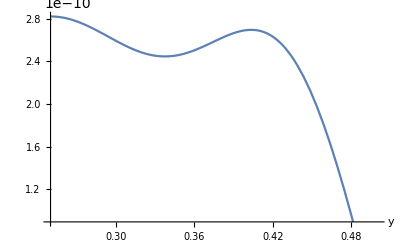

```mathematica
Plot[σx/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.0005,e->7.05*10^10, x->0.4},{y,0.25,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

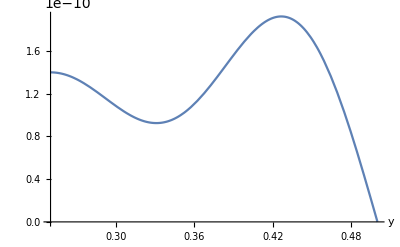

```mathematica
Plot[σy/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.0005,e->7.05*10^10, x->0.4},{y,0.25,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

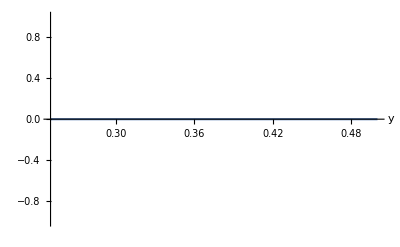

```mathematica
Plot[thauzx/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.0005,e->7.05*10^10, x->0.4},{y,0.25,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```

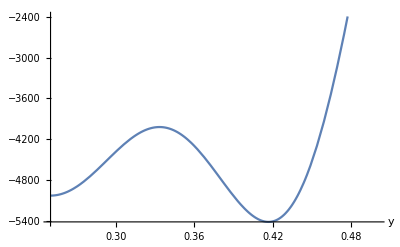

```mathematica
Plot[maxthau/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345,z-> 0.0005,e->7.05*10^10, x->0.4},{y,0.25,0.5},AxesLabel->Automatic]/.{q->1,d-> d1,a->0.4,b->0.5,ν->0.345}
```